# Homework 8

## Marvyn Bailly

## Question 1

#### Part A

We wish to compute the Floquet discriminant

```mathematica
Clear[δ,ϵ]
Γ[δ_, ϵ_, ω_] = 2*Cosh[Sqrt[δ + ϵ]*T/2]*Cosh[Sqrt[δ - ϵ]*(T/2)] + (Divide[Sqrt[δ + ϵ],Sqrt[δ - ϵ]]+Divide[Sqrt[δ - ϵ],Sqrt[δ + ϵ]])*Sinh[Sqrt[δ + ϵ]*T/2]*Sinh[Sqrt[δ - ϵ]*T/2]/. T->(2*Pi)/ω
```

2 Cosh[(π √(δ-ϵ))/ω] Cosh[(π √(δ+ϵ))/ω]+((√(δ-ϵ))/(√(δ+ϵ))+(√(δ+ϵ))/(√(δ-ϵ))) Sinh[(π √(δ-ϵ))/ω] Sinh[(π √(δ+ϵ))/ω]

Plot when δ >ϵ

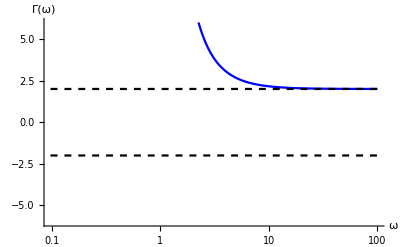

```mathematica
(* d = 0.001, e=0.02 *)
Clear[δ,ϵ]
δ = 0.4;
ϵ = 0.1;
LogLinearPlot[{Γ[δ,ϵ,ω],2,-2},{ω,0,100},
	PlotRange->{{0,100},{-6,6}},
	PlotStyle->{{Blue},{Black,Dashed},{Black,Dashed}},
	AxesLabel->{"ω","Γ(ω)"}]
```

Plot when δ < ϵ

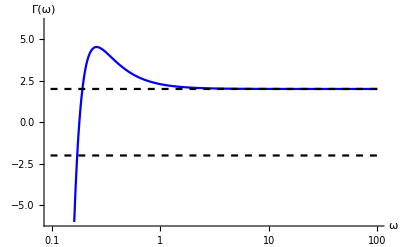

```mathematica
Clear[δ,ϵ]
δ = 0.0075;
ϵ = 0.02;
LogLinearPlot[{Γ[δ,ϵ,ω],2,-2},{ω,0,100},
	PlotRange->{{0,100},{-6,6}},
	PlotStyle->{{Blue},{Black,Dashed},{Black,Dashed}},
	AxesLabel->{"ω","Γ(ω)"}]
```